```mathematica
Needs["ErrorBarPlots`"]
```

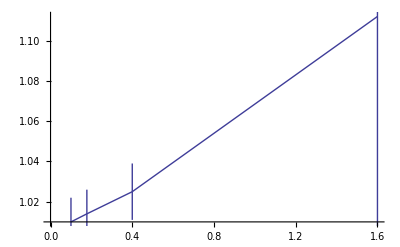

```mathematica
ErrorListPlot[{{{100/(100*10),1.01},ErrorBar[0.012]},{{100/(75*7.5),1.014},ErrorBar[0.012]},{{100/(50*5),1.025},ErrorBar[0.014]},{{100/(25*2.5),1.112},ErrorBar[0.140]}},{Joined->True,DataRange->{-100,100}}]
```

```mathematica
ListPlot[{{100/(100*10),1.01},{100/(75*7.5),1.014},{100/(50*5),1.025},{100/(25*2.5),1.112}},{Joined->True,ImageSize->Large,AxesLabel->{"Number density","Crossing time (normalized)"}}]
```

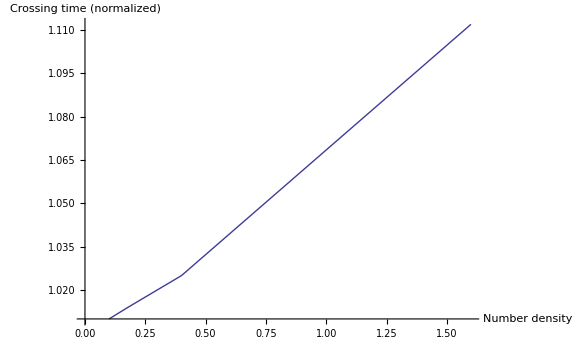

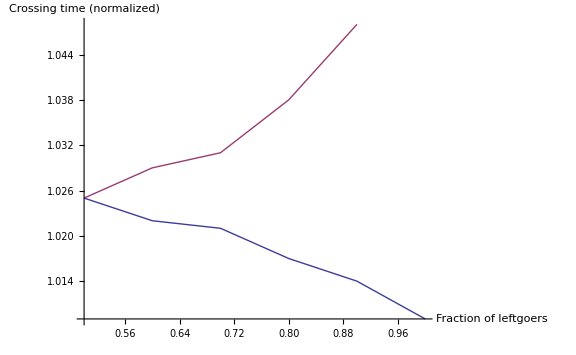

```mathematica
ListPlot[{{{0.5,1.025},{0.6,1.022},{0.7,1.021},{0.8,1.017},{0.9,1.014},{1.0,1.009}},{{0.5,1.025},{0.6,1.029},{0.7,1.031},{0.8,1.038},{0.9,1.048}}},{Joined->True,ImageSize->Large,AxesLabel->{"Fraction of leftgoers","Crossing time (normalized)"}}]
```